```mathematica
vk=0.84; (*конечная скорость*)
 a=0.; (*ускорение*)
ϵ=10^-10; (*погрешность*)
t0=15; (*время разгона*)
```

```mathematica
s [t_]:=vk t; (*координата от времени*)
v[t_]:=vk; (*скорость от времени*)
w[t_]:=0; (*ускорение*)

tzap[x_,y_,t_]:=Module[{t1,t2},
t1=t; t2=t-2ϵ;
While[Abs[t1-t2]>ϵ,t1=t2;t2=t-√((x-s[t1])^2+y^2)]; (*расчет итерациями запаздывающего момента*)
t2
]; (*tzap*)

rlw[x_,y_,t_]:=Module[{t2,r,nx,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; k=1-nx v[t2];
k)
]; (*phi*)

phi[x_,y_,t_]:=Module[{t2,r,nx,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; k=1-nx v[t2];
1/k^3)
]; (*phi*)
electr[x_,y_,t_]:=Module[{t2,r,nx,ny,n,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; ny=y/r; n={nx,ny};k=1-nx v[t2];
1/k^3((1-v[t2]^2+r nx w[t2])/r^2(n-{v[t2],0})-k/r{w[t2],0})
]; (*эл. поле*)
electrM[x_,y_,t_]:=Module[{ee},
ee=electr[x,y,t];
√(ee.ee)
]; (*его модуль*)
```

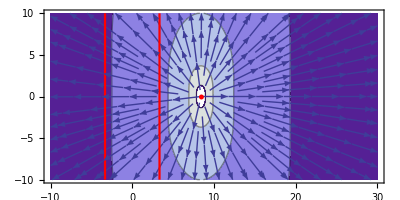

```mathematica
t=10;
Show[
ContourPlot[electrM[x,y,t],{x,-10,30},{y,-10,10},Contours->Table[k,{k,-100,100,1}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electr[x,y,t],{x,-10,30},{y,-10,10},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

```mathematica
ss=Monitor[Table[
Show[
ContourPlot[electrM[x,y,t],{x,-10,30},{y,-10,10},Contours->Table[k,{k,-100,100,1}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electr[x,y,t],{x,-10,30},{y,-10,10},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
],
{t,0,20,0.25}],
t];
```

```mathematica
Export["D://lw-electr-v=const_not_log.gif",ss]
```

D://lw-electr-v=const.gif